InterpolatingFunction[{{0.,10.}},<>][t]

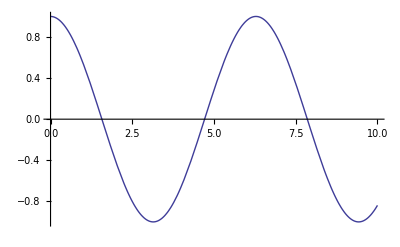

```mathematica
(*Solving differential equations numerically*)
(*Pure function solution*)
w=1;deq=x''[t]+w^2*x[t]==0;
nsol=NDSolve[{deq,x'[0]==0,x[0]==1},x[t],{t,0,10}];
nsol=x[t]/.nsol[[1]]
Plot[nsol,{t,0,10}]
```

0.877583

-0.479425

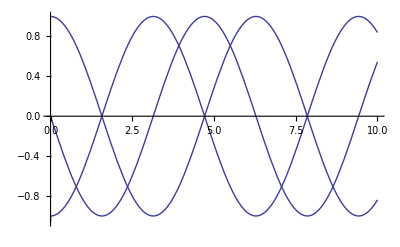

```mathematica
(*Non-Pure function solution*)
w=1;deq=x''[t]+w^2*x[t]==0;
nsol=NDSolve[{deq,x'[0]==0,x[0]==1},x,{t,0,10}];
(*x[0.5]=?*)
xatp5=x[0.5]/.nsol[[1]]
fderx=x'[0.5]/.nsol[[1]]
Plot[{x[t],x'[t],x''[t]}/.nsol[[1]],{t,0,10}]
```

Cos[t]

InterpolatingFunction[{{0.,10.}},<>][t]

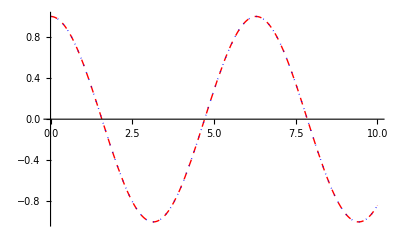

```mathematica
(*exact solution and numerical solution*)
w=1;deq=x''[t]+w^2*x[t]==0;
nsol=NDSolve[{deq,x'[0]==0,x[0]==1},x[t],{t,0,10}];
sol=DSolve[{deq,x'[0]==0,x[0]==1},x[t],t];
sol=x[t]/.sol[[1]]
nsol=x[t]/.nsol[[1]]
Plot[{nsol,sol},{t,0,10},PlotStyle->{{Red,Dashed},{Blue,Dotted,Thick}}]
```